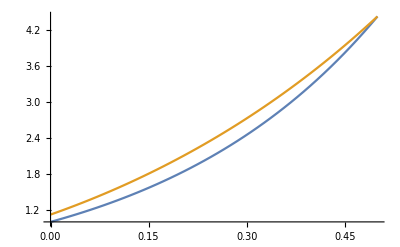

```mathematica
Plot[{1/27(2+25 E^(3t)+6t+9 t^2),0.549574 E^-t(4.72222-5.45878 E^t+2.77778 E^(3t)+0.666667t+5.45878 E^t t+t^2)},{t,0,0.5}]
```

```mathematica
f[x_,y_]:=3y-x^2;
g[x_,z_]:=-z+3x;

h=0.1;
Subscript[y, i]=1;
p1=1;

For[Subscript[x, i]=0,Subscript[x, i]<0.5,Subscript[x, i]+=h,
	k1=h*f[Subscript[x, i],Subscript[y, i]];
	Subscript[y, i] += k1*p1;
];
Print["y_i = ",Subscript[y, i]];
Subscript[z, i]=Subscript[y, i];
For[Subscript[x, i]=0.4,Subscript[x, i]≥0,Subscript[x, i]-=h,
	k1=-h*g[Subscript[x, i],Subscript[z, i]];
	Subscript[z, i]+=k1*p1;
];
Print["z_i = ",Subscript[z, i]];
```

y_i = 3.67627

z_i = 5.51959

```mathematica
Subscript[y, i]=1;
p1=1/2;
p2=1/2;

For[Subscript[x, i]=0,Subscript[x, i]<0.5,Subscript[x, i]+=h,
	k1=h*f[Subscript[x, i],Subscript[y, i]];
	k2=h*(f[Subscript[x, i]+h,Subscript[y, i]+k1]);
	Subscript[y, i] += k1*p1 + k2*p2;
];
Print["y_i = ",Subscript[y, i]];
Subscript[z, i]=Subscript[y, i];
For[Subscript[x, i]=0.4,Subscript[x, i]≥0,Subscript[x, i]-=h,
	k1=-h*g[Subscript[x, i],Subscript[z, i]];
	k2=-h*(g[Subscript[x, i]-h,Subscript[y, i]+k1]);
	Subscript[z, i]+=k1*p1+k2*p2;
];
Print["z_i = ",Subscript[z, i]];
```

y_i = 4.33915

z_i = 6.59526

```mathematica
Subscript[y, i]=1;
p1=1/6;
p2=1/3;
p3=1/3;
p4=1/6;

For[Subscript[x, i]=0,Subscript[x, i]<0.5,Subscript[x, i]+=h,
	k1=h*f[Subscript[x, i],Subscript[y, i]];
	k2=h*f[Subscript[x, i]+h/2,Subscript[y, i]+k1/2];
	k3=h*f[Subscript[x, i]+h/2,Subscript[y, i]+k2/2];
	k4=h*f[Subscript[x, i]+h,Subscript[y, i]+k3];
	
	Subscript[y, i] += k1*p1 + k2*p2+k3*p3+k4*p4;
];
Print["y_i = ",Subscript[y, i]];
Subscript[z, i]=Subscript[y, i];
For[Subscript[x, i]=0.4,Subscript[x, i]≥0,Subscript[x, i]-=h,
	k1=-h*g[Subscript[x, i],Subscript[y, i]];
	k2=-h*g[Subscript[x, i]-h/2,Subscript[y, i]+k1/2];
	k3=-h*g[Subscript[x, i]-h/2,Subscript[y, i]+k2/2];
	k4=-h*g[Subscript[x, i]-h,Subscript[y, i]+k3];
	Subscript[z, i]+=k1*p1+k2*p2+k3*p3+k4*p4;
];
Print["z_i = ",Subscript[z, i]];
```

y_i = 4.41788

z_i = 6.5031